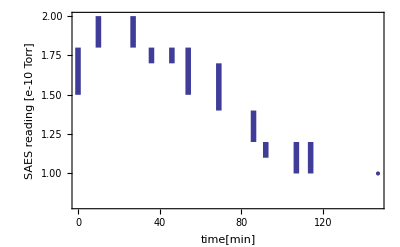

```mathematica
Needs["ErrorBarPlots`"]
Ints= {{1.5,1.8},{1.8,2.0},{1.8,2.0},{1.7,1.8},{1.7,1.8},{1.5,1.8},{1.4,1.7},{1.2,1.4},{1.1,1.2},{1.0,1.2},{1.0,1.2},{1.0,1.0}};

meanpressures=Mean[#]&/@Ints;
Errs=(Differences[#]/2)[[1]]&/@Ints;
errbars=ErrorBar[#]&/@Errs;
times={0,10,27,36,46,54,69,86,92,107,114,147};
dat=Thread[{times,meanpressures}];
daterr=Thread[{dat,errbars}];
ErrorListPlot[daterr,PlotRange->{All,{.8,2}},Frame->True,FrameLabel->{"time[min]","SAES reading [e-10 Torr]"},PlotStyle->{Thickness[0.01]}]
```